```mathematica
(*Radius of Sphere one*)
r1=1.;
(*Radius of Sphere two*)
r2=1.;
(*Distance between the centres of the spheres*)
R=3.5;
(*maximal ell in the basis of vector-spherical harmonics*)
NN=6;
logdet[λλ_]:=(
(*value of lambda, not here real values correspond to the positive imaginary line*)
λ=λλ;
rad=r1{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
(*radius vector on sphere two*)
radp=r2{Sin[θp]Cos[ϕp],Sin[θp]Sin[ϕp], Cos[θp]}+{0,0,R};
(*vector spherical harmonics on  sphere one*)
(*t1 is the spherical harmonic U and Psi; t2 corresponds to Vm and Phi*)
(*note that these form an orthonormal basis on the unit sphere*)
basis[ell_,m_]=SphericalHarmonicY[ell,m,θ,ϕ];
basisp[ell_,m_]=basis[ell,m]/.{θ->θp,ϕ->ϕp};
(*List of possible indices for the vector spherical harmonics in format (ell,m,p)*)
indexlist=Flatten[Table[Table[{ell,m},{m,-ell,ell}],{ell,0,NN}],1];
(*index the list by natural numbers*)
mp[k_]:=indexlist[[k]];
(*Computation of the Matrix-Green's function*)
dxxp=Sqrt[(x-xp)^2+(y-yp)^2+(z-zp)^2];
(*scalar Greens function*)
green[rr_]=(Exp[λ I rr])/(4 Pi rr);
(*the kernel function expressed in spherical coordinates on the two spheres*)
kerfun=green[dxxp]/.{x->rad[[1]],y->rad[[2]],z->rad[[3]],xp->radp[[1]],yp->radp[[2]],zp->radp[[3]]};
MatDiag1=DiagonalMatrix[Table[-1/((D[SphericalHankelH1[mp[k][[1]],λ rr],rr]/SphericalHankelH1[mp[k][[1]],λ rr])-(D[SphericalBesselJ[mp[k][[1]],λ rr],rr]/SphericalBesselJ[mp[k][[1]],λ rr]))/.{rr->r1},{k,1,Length[indexlist]}]];
MatOffDiag[k1_,k2_]:=(
ind1=mp[k1];
ind2=mp[k2];
If[ind1[[2]]==ind2[[2]],result=2Pi Quiet[NIntegrate[basis[ind1[[1]],ind1[[2]]]kerfun basisp[ind2[[1]],ind2[[2]]]*Sin[θ]Sin[θp]/.{ϕp->0.},{θ,0,Pi},{ϕ,0,2Pi},{θp,0,Pi},Method->"MultiPeriodic",AccuracyGoal->8]],result=0.];result);
MM=Length[indexlist];
A =MatDiag1;
B=ParallelTable[MatOffDiag[j,k],{k,1,MM},{j,1,MM}];
Log[Det[IdentityMatrix[MM]-Inverse[A].Transpose[B].Inverse[A].B]]
);
```

{0.0001,-0.106576+4.53072×10^-18 ⅈ}

{0.1001,-0.0718612-6.95479×10^-18 ⅈ}

{0.2001,-0.0495641-1.65161×10^-18 ⅈ}

{0.3001,-0.0347136-3.60642×10^-18 ⅈ}

{0.4001,-0.0245764-1.62325×10^-18 ⅈ}

{0.5001,-0.0175364-1.88372×10^-18 ⅈ}

{0.6001,-0.0125867-4.60089×10^-19 ⅈ}

{0.7001,-0.00907489-6.36513×10^-19 ⅈ}

{0.8001,-0.00656605-5.46399×10^-19 ⅈ}

{0.9001,-0.00476424-7.40794×10^-20 ⅈ}

{1.0001,-0.00346483-3.29337×10^-19 ⅈ}

{1.1001,-0.00252461-1.23262×10^-19 ⅈ}

{1.2001,-0.00184246-5.61778×10^-20 ⅈ}

{1.3001,-0.00134644-8.07688×10^-20 ⅈ}

{1.4001,-0.000985092-2.48279×10^-20 ⅈ}

{1.5001,-0.000721438-2.55546×10^-20 ⅈ}

{1.6001,-0.000528808-2.16556×10^-20 ⅈ}

{1.7001,-0.000387906-1.16646×10^-20 ⅈ}

{1.8001,-0.00028474-9.23161×10^-21 ⅈ}

{1.9001,-0.000209136-1.56744×10^-20 ⅈ}

{2.0001,-0.000153688-1.22393×10^-20 ⅈ}

{2.1001,-0.000112994-4.51675×10^-21 ⅈ}

{2.2001,-0.0000831115-3.45057×10^-21 ⅈ}

{2.3001,-0.0000611551-3.41531×10^-21 ⅈ}

{2.4001,-0.0000450149-1.63773×10^-21 ⅈ}

{2.5001,-0.000033145-1.02298×10^-21 ⅈ}

{2.6001,-0.000024412-1.26187×10^-21 ⅈ}

{2.7001,-0.0000179847-4.11671×10^-22 ⅈ}

{2.8001,-0.0000132528-5.20494×10^-22 ⅈ}

{2.9001,-9.76796×10^-6-6.59011×10^-22 ⅈ}

{3.0001,-7.20091×10^-6-4.79925×10^-22 ⅈ}

{3.1001,-5.30945×10^-6-2.70486×10^-22 ⅈ}

{3.2001,-3.91547×10^-6-6.18519×10^-23 ⅈ}

{3.3001,-2.88791×10^-6-1.4475×10^-22 ⅈ}

{3.4001,-2.13031×10^-6-8.88555×10^-23 ⅈ}

{3.5001,-1.57165×10^-6-4.74758×10^-23 ⅈ}

{3.6001,-1.15963×10^-6-4.09766×10^-23 ⅈ}

{3.7001,-8.55715×10^-7-3.81104×10^-23 ⅈ}

{3.8001,-6.31508×10^-7-2.56425×10^-23 ⅈ}

{3.9001,-4.66086×10^-7-1.88827×10^-23 ⅈ}

{4.0001,-3.44022×10^-7-3.71409×10^-24 ⅈ}

{4.1001,-2.53944×10^-7-1.66455×10^-23 ⅈ}

{4.2001,-1.87463×10^-7-6.52772×10^-24 ⅈ}

{4.3001,-1.38395×10^-7-3.76837×10^-24 ⅈ}

{4.4001,-1.02175×10^-7-2.53564×10^-24 ⅈ}

{4.5001,-7.54376×10^-8-3.05154×10^-24 ⅈ}

{4.6001,-5.56993×10^-8-2.57142×10^-24 ⅈ}

{4.7001,-4.11269×10^-8-1.54852×10^-24 ⅈ}

{4.8001,-3.03679×10^-8-9.47281×10^-25 ⅈ}

{4.9001,-2.24241×10^-8-8.78562×10^-25 ⅈ}

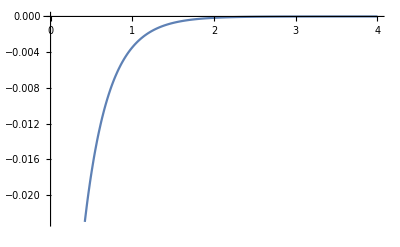

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00467752-2.95297×10^-19 ⅈ

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0430362-2.5296×10^-18 ⅈ

```mathematica
tbl={};
Do[
{val=logdet[I lam],AppendTo[tbl,{lam,val}],Print[{lam,val}]},{lam,0.0001,5,0.1}]
f=Interpolation[tbl,InterpolationOrder->3];
Plot[f[lam],{lam,0.0,4}]
NIntegrate[f[lam],{lam,0,4}]/(2Pi)
```

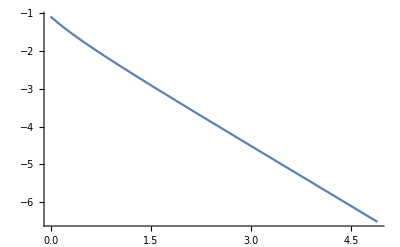

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0433888-2.53601×10^-18 ⅈ

```mathematica
Plot[Log[-f[lam]],{lam,0.0,4.9},PlotRange->All]
NIntegrate[f[lam],{lam,0,4.9}]/(2Pi)
```

General::prng: Value of option PlotRange -> {} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

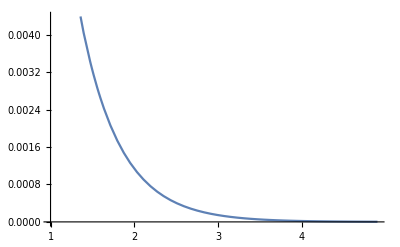

```mathematica
Plot[-f[lam]/Exp[-lam],{lam,1,4.9},PlotRange->{}]
```

```mathematica
Fit[Table[{lam,Log[f[lam]]},{lam,4,4.9,0.1}],{x,1},x]
```

(-2.74688-3.14159 ⅈ)-(3.03391+3.7791×10^-16 ⅈ) x

```mathematica
Log[a Exp[-b x]] = Log[a] - b x
```

```mathematica
Exp[-2.746877478338795]
```

0.0641278

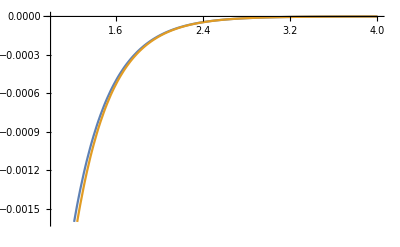

```mathematica
Plot[{-Exp[(-2.746877478338795)-(3.033914514010481)x],f[x]},{x,1,4}]
```